Stress Cube Diagram

Input stress tensor (generalized plane stress)

```mathematica
ClearAll["Global`*"]
```

```mathematica
sigma={{7,4,0},{4,2,0},{0,0,-1}};
sigma={{-4,4,0},{4,2,0},{0,0,-1}};
sigma={{4,5,0},{5,-3,0},{0,0,8}};
sigma={{-40,0,0},{0,-10,30},{0,30,-20}};
sigma={{-40,0,30},{0,-10,0},{30,0,-20}};
sigma=N[{{-40,0,30},{0,-10,0},{30,0,-20}}];
sigma={{4,5,0},{5,-3,0},{0,0,8}};
sigma//MatrixForm
```

(4 | 5 | 0
5 | -3 | 0
0 | 0 | 8)

Determine which plane shear stress is in

```mathematica
If[sigma[[1,2]]≠0,plane="xy"]
If[sigma[[1,3]]≠0,plane="xz"]
If[sigma[[2,3]]≠0,plane="yz"]
```

xy

Find points of interest; dependent on which plane the shear stress is in

This assigns values to givenpoints[[]] (several points on the circle), center, and radius

```mathematica
If[plane=="xy",{givenpoints={{sigma[[1,1]],-sigma[[1,2]]},{sigma[[2,2]],sigma[[1,2]]},{sigma[[3,3]],0}},center=(sigma[[1,1]]+sigma[[2,2]])/2,radius=Sqrt[((sigma[[1,1]]-sigma[[2,2]])/2)^2+sigma[[1,2]]^2]}];
If[plane=="xz",{givenpoints={{sigma[[1,1]],sigma[[1,3]]},{sigma[[2,2]],0},{sigma[[3,3]],-sigma[[1,3]]}},center=(sigma[[1,1]]+sigma[[3,3]])/2,radius=Sqrt[((sigma[[1,1]]-sigma[[3,3]])/2)^2+sigma[[1,3]]^2]}];
If[plane=="yz",{givenpoints={{sigma[[1,1]],0},{sigma[[2,2]],-sigma[[2,3]]},{sigma[[3,3]],sigma[[2,3]]}},center=(sigma[[2,2]]+sigma[[3,3]])/2,radius=Sqrt[((sigma[[2,2]]-sigma[[3,3]])/2)^2+sigma[[2,3]]^2]}];
```

Find principle stresses and (smallest) angle to principle plane

This computes principal normal stresses

```mathematica
If[plane=="xy",
{sigmaP1=center+radius,
sigmaP2=center-radius,
sigmaP3=sigma[[3,3]]}];
If[plane=="xz",
{sigmaP1=center+radius,
sigmaP2=sigma[[2,2]],
sigmaP3=center-radius}];
If[plane=="yz",
{sigmaP1=sigma[[1,1]],
sigmaP2=center+radius,
sigmaP3=center-radius}];
N[{sigmaP1,sigmaP2,sigmaP3}]
```

{6.60328,-5.60328,8.}

Find (smallest) angle to principle planes

```mathematica
minzero[x_]:={min=Max[Abs[x]];
For[n=1,n≤Length[x],n++,
If[ Abs[ x[[n]] ]<Abs[min],min=x[[n]] ]
 ];
min};
givenpoints
center
thetaP1=(1/2)*ArcTan[( givenpoints[[1,1]]-center ),givenpoints[[1,2]]]
thetaP2=(1/2)*ArcTan[( givenpoints[[2,1]]-center ),givenpoints[[2,2]]]
```

{{4,-5},{-3,5},{8,0}}

1/2

-1/2 ArcTan[10/7]

1/2 (π-ArcTan[10/7])

Display output

Compute display parameters

Displaycenter is the center of the viewing area; displaydim is a vector containing half the display width, half the display height; displayrange is formatted {{xmin, xmax},{ymin, ymax}};
Displayelement is a small length characteristic of the size of the display (this helps with scaling the graphics appropriately); numtics is the number of ticks to show along each axis;
Tickspacingx is the spacing between ticks based on numticks and the display range

```mathematica
displaycenter={(Min[sigmaP1,sigmaP2,sigmaP3]+Max[sigmaP1,sigmaP2,sigmaP3])/2,0};
displaydim=1.5*.5*{Max[sigmaP1,sigmaP2,sigmaP3]-Min[sigmaP1,sigmaP2,sigmaP3],2*radius};
displayrange={{displaycenter[[1]]-displaydim[[1]],displaycenter[[1]]+displaydim[[1]]},{displaycenter[[2]]-displaydim[[2]],displaycenter[[2]]+displaydim[[2]]}};
displayelement=.1*((displaydim[[1]]+displaydim[[2]])/2);

numticks=10;
tickspacingx=Abs[ displayrange[[1,2]]-displayrange[[1,1]] ]/numticks;
tickspacingy=Abs[ displayrange[[2,2]]-displayrange[[2,1]] ]/numticks;
```

Circles

First the circle for the faces of the unrotated stress cube is determined. Then the other two circles are found such that they intersect the remaining principal stresses. The circle information is put in a generic circledata array, to be used to generate the graphics primitives.

```mathematica
If[plane=="xy",
circledata={{center,0,radius},{(sigmaP2+sigmaP3)/2,0,Abs[sigmaP2-sigmaP3]/2},{(sigmaP1+sigmaP3)/2,0,Abs[sigmaP1-sigmaP3]/2}}];
If[plane=="xz",
circledata={{center,0,radius},{(sigmaP1+sigmaP2)/2,0,Abs[sigmaP1-sigmaP2]/2},{(sigmaP2+sigmaP3)/2,0,Abs[sigmaP2-sigmaP3]/2}}];
If[plane=="yz",
circledata={{center,0,radius},{(sigmaP1+sigmaP2)/2,0,Abs[sigmaP1-sigmaP2]/2},{(sigmaP1+sigmaP3)/2,0,Abs[sigmaP1-sigmaP3]/2}}];
```

The largest circle is determined. circledata[[largestcircle]] is then the row containing enough information to draw the largest circle.

```mathematica
largestcircle=1;
rowmax=Dimensions[circledata,1];
For[row=1,row≤rowmax[[1]],row++,
{
If[circledata[[row,3]]>circledata[[largestcircle,3]],largestcircle=row]
}
]
```

Finally the graphics objects are created, all three circles in one foul swoop. Since all graphics objects in the show command follow the formatting rules set by the first, and the circle object is always shown in the graphics output, it was chosen to contain all plot formatting information, such as axis labels and tick marks.

```mathematica
circle1:=Graphics[{Circle[{circledata[[1,1]],circledata[[1,2]]},circledata[[1,3]]],
Circle[{circledata[[2,1]],circledata[[2,2]]},circledata[[2,3]]],
Circle[{circledata[[3,1]],circledata[[3,2]]},circledata[[3,3]]]},
Axes->True,
AxesLabel->{Subscript[σ,nn],Subscript[σ,ns]},
LabelStyle->Directive[Large,Bold],
Ticks->{ Floor[ Table[tickspacingx*Floor[.5*n]*(-1)^Floor[1.5*n],{n,0,Ceiling[(2*Max[Abs[ displayrange[[1]] ]]+1)/tickspacingx]}] ], Floor[ Table[tickspacingy*Floor[.5*n]*(-1)^Floor[1.5*n],{n,0,Ceiling[(2*Max[Abs[ displayrange[[2]] ]]+1)/tickspacingy]}] ] },
TicksStyle->Directive[Small,Italic],
PlotRange->displayrange,
AspectRatio->1];
```

Lines

This creates the line graphics object which draws a line from the appropriate points related to the faces of the unrotated stress cube.

```mathematica
If[plane=="xy",
line1:=Graphics[Line[ {givenpoints[[1]],givenpoints[[2]]} ]] ];
If[plane=="xz",
line1:=Graphics[Line[ {givenpoints[[1]],givenpoints[[3]]} ]] ];
If[plane=="yz",
line1:=Graphics[Line[ {givenpoints[[2]],givenpoints[[3]]} ]] ];
```

Points

Pointsdata is an array of two-element vectors representing points to be displayed. The order of the points in this array is identical to the order in which they are assigned annotation elements.

```mathematica
pointsdata={ givenpoints[[1]],givenpoints[[2]],givenpoints[[3]],{center,0}, {sigmaP1,0}, {sigmaP2,0}, {sigmaP3,0},{circledata[[largestcircle,1]],circledata[[largestcircle,3]]},{circledata[[largestcircle,1]],-circledata[[largestcircle,3]]} };
```

A graphics object to generate a plot of all points is next created.

```mathematica
points1:=Graphics[
{PointSize[Large],Red,Point[pointsdata]}
];
```

Annotation

Create r1, a set of vectors pointing from the origin to the points to be annotated

```mathematica
r1=N[ pointsdata-ConstantArray[displaycenter,Dimensions[pointsdata,1]] ];
dim=Dimensions[r1,1];
r1norm=N[ Table[ {Norm[ r1[[i]] ],Norm[  r1[[i]] ]},{ i,dim[[1]] } ] ];
```

Create r2, a set of vectors pointing from the points to be annotated out a small distance away from the points

```mathematica
r2=ConstantArray[{0,0},dim[[1]]];
For[row=1,row≤dim[[1]],row++,
If[ r1norm[[row,1]]≠0,r2[[row]]=displayelement*r1[[row]]/r1norm[[row]] ]
]
```

Create annotationdata, the array of points at which annotations will eventually be placed. The points in annotationdata are slightly offset from those in pointsdata, so that the annotations do not overlap the points.

```mathematica
annotationdata=ConstantArray[displaycenter,Dimensions[pointsdata,1]]+r1+r2;
```

Debug annotationdata; move annotation elements that are near axes away from those axes

```mathematica
dim=Dimensions[annotationdata,1];
For[row=1,row≤dim[[1]],row++,{
If[ Abs[annotationdata[[row,1]] ]<displayelement,
{ annotationdata[[row,1]]=displayelement*(2*Ceiling[(Sign[annotationdata[[row,1]]]+1)/2]-1),
r2[[row]]=annotationdata[[row]]-pointsdata[[row]] }
],
If[ Abs[annotationdata[[row,2]] ]<displayelement,
{ annotationdata[[row,2]]=displayelement*(2*Ceiling[(Sign[annotationdata[[row,2]]]+1)/2]-1),
r2[[row]]=annotationdata[[row]]-pointsdata[[row]] }
]
}];
```

Determine which points in annotationdata are "duplicates", where a "duplicate" pair of pionts are two points separated by no more than the length displayelement.

```mathematica
duplicates={};
temparray=annotationdata;
dim=Dimensions[temparray,1];
For[row1=1,row1≤dim[[1]]-1,row1++,
{temp={row1},
For[row2=row1+1,row2≤dim[[1]],row2++,
If[EuclideanDistance[ temparray[[row2]],temparray[[row1]] ]≤displayelement&&temparray[[row2]]≠{},
{temp=Append[temp,row2],temparray[[row2]]={}}
]
],
If[ Length[temp]>1,duplicates=Append[duplicates,temp] ]}
]
```

Step through the rows of the duplicates[[]] array, and separate all points that are considered "overlapping". All r2 vectors associated with the points in the rows of duplicates[[]] are rotated to generate an angular spread.

```mathematica
rmatrix[theta_]={{Cos[theta],Sin[theta]},{-Sin[theta],Cos[theta]}};
dim=Dimensions[duplicates,1];
For[row=1,row≤dim[[1]],row++,
{numcollisions=Length[ duplicates[[row]] ],
If[ numcollisions>1,
{spread=(Pi/6)*(Range[0,numcollisions-1]-N[ Median[ Range[ 0, numcollisions-1 ] ] ]),
For[col=1,col≤Length[ duplicates[[row]] ],col++,
r2[[ duplicates[[row,col]] ]]=r2[[ duplicates[[row,col]] ]].rmatrix[ spread[[col]] ]
]}
]}
]

annotationdata=ConstantArray[displaycenter,Dimensions[pointsdata,1]]+r1+r2;
```

Create graphics objects that will draw annotation elements at the points contained within annotationdata

```mathematica
annotation1:=Graphics[Text[Style["x-face",Larger,Blue],annotationdata[[1]] ]];
annotation2:=Graphics[Text[Style["y-face",Larger,Blue],annotationdata[[2]] ]];
annotation3:=Graphics[Text[Style["z-face",Larger,Blue],annotationdata[[3]] ]];
annotation4:=Graphics[Text[Style["Center",Larger,Blue],annotationdata[[4]] ]];
annotation5:=Graphics[Text[Style[Subscript[σ,P1],Larger,Blue],annotationdata[[5]] ]];
annotation6:=Graphics[Text[Style[Subscript[σ,P2],Larger,Blue],annotationdata[[6]] ]];
annotation7:=Graphics[Text[Style[Subscript[σ,P3],Larger,Blue],annotationdata[[7]] ]];
annotation8:=Graphics[Text[Style[Subscript[σ,smax],Larger,Blue],annotationdata[[8]] ]];
annotation9:=Graphics[Text[Style[Subscript[σ,smin],Larger,Blue],annotationdata[[9]] ]];
```

Display

Show graphical output, followed by the values of the points.

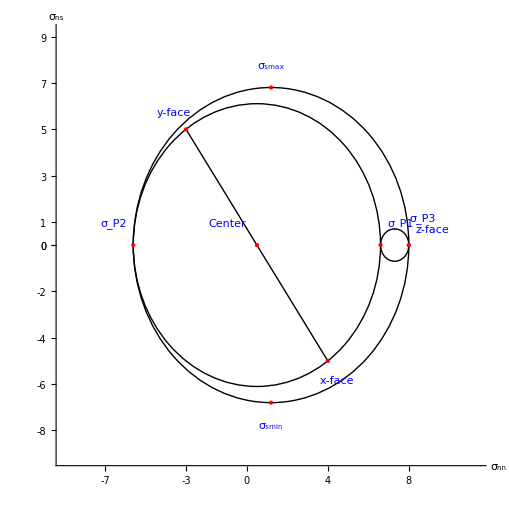

{(σ =  | (4. | 5. | 0.
5. | -3. | 0.
0. | 0. | 8.)),(x-face | {4,-5}
y-face | {-3,5}
z-face | {8,0}
Center | {1/2,0}
σ_P1 | {1/2+(√149)/2,0}
σ_P2 | {1/2-(√149)/2,0}
σ_P3 | {8,0}
σ_smax | {1/2 (17/2-(√149)/2),1/2 (15/2+(√149)/2)}
σ_smin | {1/2 (17/2-(√149)/2),1/2 (-15/2-(√149)/2)}),(x-face | {4.,-5.}
y-face | {-3.,5.}
z-face | {8.,0.}
Center | {0.5,0.}
σ_P1 | {6.60328,0.}
σ_P2 | {-5.60328,0.}
σ_P3 | {8.,0.}
σ_smax | {1.19836,6.80164}
σ_smin | {1.19836,-6.80164})}

```mathematica
Show[circle1,line1,points1,annotation1,annotation2,annotation3,annotation4,annotation5,annotation6,annotation7,annotation8,annotation9]

{{{"σ = ",N[sigma]//MatrixForm}}//MatrixForm,
{{"x-face",pointsdata[[1]]},
{"y-face",pointsdata[[2]]},
{"z-face",pointsdata[[3]]},
{"Center",pointsdata[[4]]},
{Subscript[σ,P1],pointsdata[[5]]},
{Subscript[σ,P2],pointsdata[[6]]},
{Subscript[σ,P3],pointsdata[[7]]},
{Subscript[σ,smax],pointsdata[[8]]},
{Subscript[σ,smin],pointsdata[[9]]}
}//MatrixForm,N[{{"x-face",pointsdata[[1]]},
{"y-face",pointsdata[[2]]},
{"z-face",pointsdata[[3]]},
{"Center",pointsdata[[4]]},
{Subscript[σ,P1],pointsdata[[5]]},
{Subscript[σ,P2],pointsdata[[6]]},
{Subscript[σ,P3],pointsdata[[7]]},
{Subscript[σ,smax],pointsdata[[8]]},
{Subscript[σ,smin],pointsdata[[9]]}
}]//MatrixForm}
```

Display parameters that may be tweaked

```mathematica
Clear["Global`*"]
dx=1;
lennn=.8;
offsetnn=.1;
lenns=.9;
offsetns=.2;

colnn={0,0,0,1};
colyz={1,0,0,1};
colxz={0,1,0,1};
colxy={0,0,1,1};
(*colyz={1,0,0,1};
colxz={1,.8,0,1};
colxy={1,0,.8,1};*)
```

Define transformaion matrices

The rotation and reflection matrices that compose the transformation matrices assume a right-handed coordinate system, with counter-clockwise rotation positive, as dictated by the right-hand rule.

Reflection matrices reflect along their axis; RF1 reflects along the x-axis (across the yz plane), and so forth.

Transformation matrices transform point sets between indicated faces; TX2Y transforms points from X-face to Y-face.

```mathematica
R1[theta_]={{1,0,0},
{0,Cos[theta],-Sin[theta]},
{0,Sin[theta],Cos[theta]}};
R2[theta_]={{Cos[theta],0,Sin[theta]},
{0,1,0},
{-Sin[theta],0,Cos[theta]}};
R3[theta_]={{Cos[theta],-Sin[theta],0},
{Sin[theta],Cos[theta],0},
{0,0,1}};
R1[θ]//MatrixForm;
R2[θ]//MatrixForm;
R3[θ]//MatrixForm;

RF1={{-1,0,0},{0,1,0},{0,0,1}};
RF2={{1,0,0},{0,-1,0},{0,0,1}};
RF3={{1,0,0},{0,1,0},{0,0,-1}};

TX2Y=RF1.R3[Pi/2];
TX2Z=RF1.R2[-Pi/2];
TY2Z=RF2.R1[Pi/2];
```

Generate sets of points necessary for display

```mathematica
(*xx,xz,xy*)
vectorscube={{{(offsetnn+1/2)*dx,0,0},{(lennn+offsetnn+1/2)*dx,0,0}},
{{(offsetns+1/2)*dx,0,-lenns*dx/2},{(offsetns+1/2)*dx,0,lenns*dx/2}},
{{(offsetns+1/2)*dx,-lenns*dx/2,0},{(offsetns+1/2)*dx,lenns*dx/2,0}}};

vectorstemp1={{TX2Y.vectorscube[[1,1]],TX2Y.vectorscube[[1,2]]},
{TX2Y.vectorscube[[2,1]],TX2Y.vectorscube[[2,2]]},
{TX2Y.vectorscube[[3,1]],TX2Y.vectorscube[[3,2]]}};

vectorstemp2={{TY2Z.vectorstemp1[[1,1]],TY2Z.vectorstemp1[[1,2]]},
{TY2Z.vectorstemp1[[2,1]],TY2Z.vectorstemp1[[2,2]]},
{TY2Z.vectorstemp1[[3,1]],TY2Z.vectorstemp1[[3,2]]}};

vectorstemp3={{TX2Z.vectorscube[[1,1]],TX2Z.vectorscube[[1,2]]},
{TX2Z.vectorscube[[2,1]],TX2Z.vectorscube[[2,2]]},
{TX2Z.vectorscube[[3,1]],TX2Z.vectorscube[[3,2]]}};

(*RX2Yxx=R3[-Pi/2];
RX2Yxz=R3[-Pi/2];
RX2Yxy=R3[-Pi/2].R1[-Pi];
vectorstemp1={{RX2Yxx.vectorscube[[1,1]],RX2Yxx.vectorscube[[1,2]]},
{RX2Yxz.vectorscube[[2,1]],RX2Yxz.vectorscube[[2,2]]},
{RX2Yxy.vectorscube[[3,1]],RX2Yxy.vectorscube[[3,2]]}};

RX2Zxx=R2[-Pi/2];
RX2Zxz=R2[-Pi/2].R1[-Pi];
RX2Zxy=R3[-Pi/2].R1[-Pi];
vectorstemp1={{RX2Yxx.vectorscube[[1,1]],RX2Yxx.vectorscube[[1,2]]},
{RX2Yxz.vectorscube[[2,1]],RX2Yxz.vectorscube[[2,2]]},
{RX2Yxy.vectorscube[[3,1]],RX2Yxy.vectorscube[[3,2]]}};*)
```

Perform all computations to get values and matrices

Draw local graphics elements

```mathematica
Graphics3D[{{RGBColor[0,.5,1,.2],Opacity[.2],

Cuboid[{-dx/2,-dx/2,-dx/2},{dx/2,dx/2,dx/2}]},
{RGBColor[colnn],Arrow[vectorscube[[1]]]},
{RGBColor[colxz],Arrow[vectorscube[[2]]]},
{RGBColor[colxy],Arrow[vectorscube[[3]]]},

{RGBColor[colnn],Arrow[vectorstemp1[[1]]]},
{RGBColor[colxz],Arrow[vectorstemp1[[2]]]},
{RGBColor[colxy],Arrow[vectorstemp1[[3]]]},

{RGBColor[colnn],Arrow[vectorstemp2[[1]]]},
{RGBColor[colxz],Arrow[vectorstemp2[[2]]]},
{RGBColor[colxy],Arrow[vectorstemp2[[3]]]},

{RGBColor[colnn],Arrow[vectorstemp3[[1]]]},
{RGBColor[colxz],Arrow[vectorstemp3[[2]]]},
{RGBColor[colxy],Arrow[vectorstemp3[[3]]]}
},
Boxed->False,
Axes->True,
AxesLabel->{"x","y","z"},
SphericalRegion->True,
ViewPoint->{1,1,1},
ViewVertical->{0,0,1},
PlotRange->All
]
```

-Graphics3D-

Draw global graphics elements

Define graphics elements for first coordinate system (C.S.)

Stress cube

```mathematica
dx=1;
dy=1;
dz=1;
```

```mathematica
cube0:=Graphics3D[{Opacity[0.5],Cuboid[{-dx/2,-dy/2,-dz/2},{dx/2,dy/2,dz/2}]},
Boxed->False,
Axes->False,
AspectRatio->1];
```

Stress vectors

```mathematica
sigmaxx:=Graphics3D[{RGBColor[tcolor],
Arrow[{surfacedata[[1,1]],surfacedata[[1,1]]+scaling*tx}],Arrow[{surfacedata[[1,2]],surfacedata[[1,2]]+scaling*ty}],Arrow[{surfacedata[[1,3]],surfacedata[[1,3]]+scaling*tz}]}];
sigmayy:=
sigmazz:=
sigmayz:=
sigmaxz:=
sigmaxy:=
```

Perform first rotation

```mathematica
If[
```

Decide which plane maximum shear is in

Perform second rotation

Editing Notes

Display Organization
Graphics Elements - Local C.S.
Geometry
-Stress cube
Stresses
-sigmaxx, sigmayy, etc.
-show stresses into/out of page properly in 2D mode
View A-A lines
Annotation
-θ_P, axes (x,y,z), θ_s, stresses, "A-A", C.S. title ("View A-A")
Axes
-(x,y,z), (x', y', z'), etc.
Graphics Elements - Global C.S.
Positioning lines
-line from ctr. of 1st cube to side o 2nd cube
-optional ghost line
-arrow indicating angular measurement
Order
1. Generate rotation matrices
2. Generate sets of points necessary for display
3. Perform all computations to obtain all values and matrices
4. Draw graphics elements local to coordinate system
 a) Draw all geometry (i.e., all three cubes)
 b) Draw stresses
 c) Draw axes
 d) Draw view A-A lines (if applicable)
 e) Draw annotation
5. Draw global graphics elements
 a) Positioning lines